```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v4\scaling\initial_v1\anum21\CEP\T50

```mathematica
lT=40;
startT=1;
alist=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/a.dat"]],{i,startT,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

```mathematica
ρmin=0;
ρmax=30000;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
rhoend=600;
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/191}];
Vall=Table[Table[Evaluate[(test=SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alist[[i]]],52])],{ρ,0,rhoend,rhoend/191}],{i,1,lT}];
Vdata=Table[Transpose[{sigma,Vall[[i]]-Vall[[i]][[1]]+10^7}],{i,1,lT}];
```

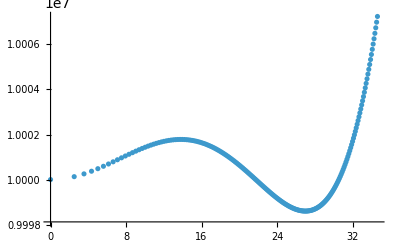

```mathematica
ListPlot[Vdata[[14;;14]],PlotRange->{All,All},ScalingFunctions->{Automatic,Automatic}]
```

```mathematica
Table[800+(i-1)1,{i,1,1}]
```

{800}